```mathematica
ClearAll["Global`*"]
```

```mathematica
l12=1;
l23=2.93;
l2=2.71;
l3=1.64;
l4=2.07;
l5=1.93;
l6=5.43;
```

```mathematica
t1Min=27;
t1Max=50;
```

```mathematica
t1=t1Min;
NSolve[{l6-l23*Cos[t1 Degree]+l4*Cos[t4 Degree]-l3*Cos[t3 Degree]+l5*Cos[t5 Degree]==0,-l23*Sin[t1 Degree]+l4*Sin[t4 Degree]-l3*Sin[t3 Degree]+l5*Sin[t5 Degree]==0,l3*Cos[t3 Degree]-l4*Cos[t4 Degree]-l12*N[Cos[t1 Degree]]+l2*Cos[t2 Degree]==0,l3*Sin[t3 Degree]-l4*Sin[t4 Degree]-l12*N[Sin[t1 Degree]]+l2*Sin[t2 Degree]==0},{t2,t3,t4,t5}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t2→94.8602,t3→-118.626,t4→157.063,t5→-151.663},{t2→94.8602,t3→-8.34654,t4→75.9647,t5→-151.663},{t2→179.587,t3→-6.78064,t4→-162.336,t5→66.111},{t2→179.587,t3→20.5401,t4→176.096,t5→66.111}}

```mathematica
solutions=Table[NSolve[{l6-l23*Cos[t1 Degree]+l4*Cos[t4 Degree]-l3*Cos[t3 Degree]+l5*Cos[t5 Degree]==0,-l23*Sin[t1 Degree]+l4*Sin[t4 Degree]-l3*Sin[t3 Degree]+l5*Sin[t5 Degree]==0,l3*Cos[t3 Degree]-l4*Cos[t4 Degree]-l12*N[Cos[t1 Degree]]+l2*Cos[t2 Degree]==0,l3*Sin[t3 Degree]-l4*Sin[t4 Degree]-l12*N[Sin[t1 Degree]]+l2*Sin[t2 Degree]==0},{t2,t3,t4,t5}],{t1,t1Min,t1Max}];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

```mathematica
Dimensions[solutions]
```

{24,4,4}

```mathematica
t1=Range[t1Min,t1Max];
```

```mathematica
set1 = solutions[[All,1,All]];
set2 = solutions[[All,2,All]];
set3 = solutions[[All,3,All]];
set4 = solutions[[All,4,All]];
```

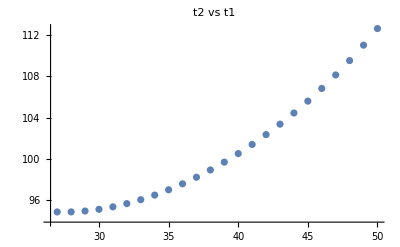

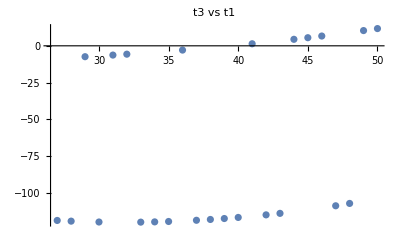

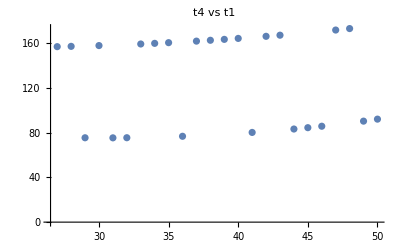

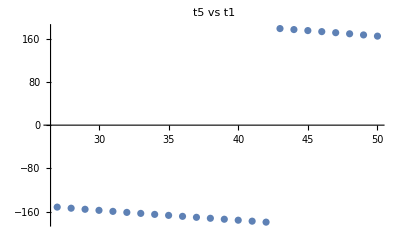

```mathematica
ListPlot[Transpose[{t1,Values[set1[[All,1]]]}],PlotLabel->"t2 vs t1"]
ListPlot[Transpose[{t1,Values[set1[[All,2]]]}],PlotLabel->"t3 vs t1"]
ListPlot[Transpose[{t1,Values[set1[[All,3]]]}],PlotLabel->"t4 vs t1"]
ListPlot[Transpose[{t1,Values[set1[[All,4]]]}],PlotLabel->"t5 vs t1"]
```

-Graphics-

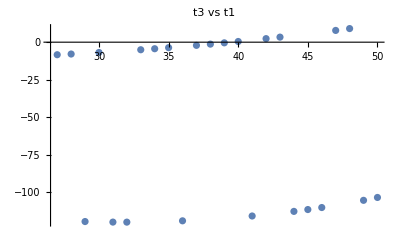

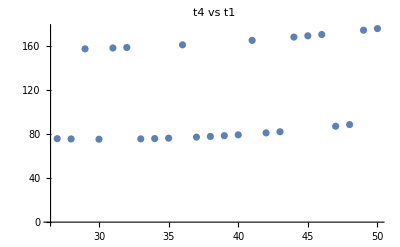

-Graphics-

```mathematica
ListPlot[Transpose[{t1,Values[set2[[All,1]]]}],PlotLabel->"t2 vs t1"]
ListPlot[Transpose[{t1,Values[set2[[All,2]]]}],PlotLabel->"t3 vs t1"]
ListPlot[Transpose[{t1,Values[set2[[All,3]]]}],PlotLabel->"t4 vs t1"]
ListPlot[Transpose[{t1,Values[set2[[All,4]]]}],PlotLabel->"t5 vs t1"]
```

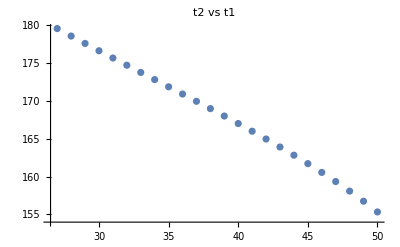

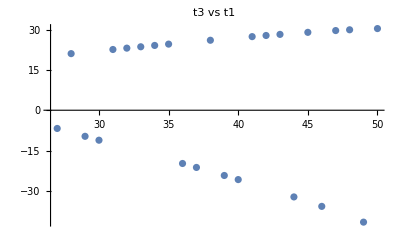

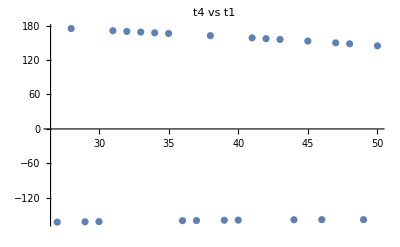

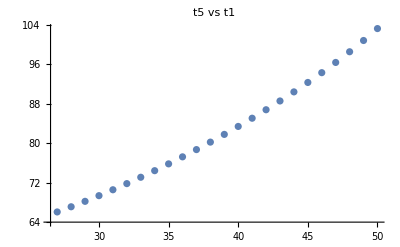

```mathematica
ListPlot[Transpose[{t1,Values[set3[[All,1]]]}],PlotLabel->"t2 vs t1"]
ListPlot[Transpose[{t1,Values[set3[[All,2]]]}],PlotLabel->"t3 vs t1"]
ListPlot[Transpose[{t1,Values[set3[[All,3]]]}],PlotLabel->"t4 vs t1"]
ListPlot[Transpose[{t1,Values[set3[[All,4]]]}],PlotLabel->"t5 vs t1"]
```

-Graphics-

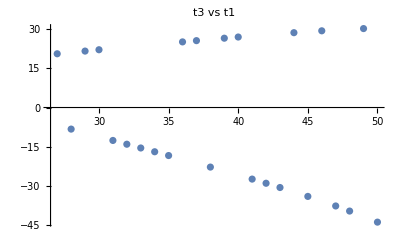

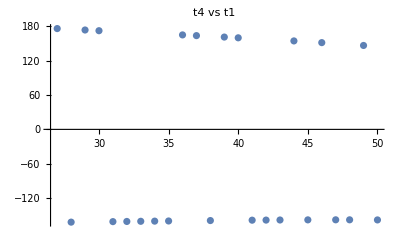

-Graphics-

```mathematica
ListPlot[Transpose[{t1,Values[set4[[All,1]]]}],PlotLabel->"t2 vs t1"]
ListPlot[Transpose[{t1,Values[set4[[All,2]]]}],PlotLabel->"t3 vs t1"]
ListPlot[Transpose[{t1,Values[set4[[All,3]]]}],PlotLabel->"t4 vs t1"]
ListPlot[Transpose[{t1,Values[set4[[All,4]]]}],PlotLabel->"t5 vs t1"]
```